# Shortfall dynamics v0

The purpose of this notebook is to build up intuition about the dynamics of the different shortfall variants. 

It is exploratory in nature and pedagogical (for the notebook author). It represents a first step, rather than comprehensive analysis, in terms of painting a picture of the shortfall landscape. 

The format is Q and A:  pose a question, answer it with an image.

## First step: define minting and pledge

Note: we don’t know exactly what minting will look like in the future.  As a first pass, let’s assume minting per sector looks like the rate today, with decreasing at the simple minting rate of decrease.  This is may be under or over optimistic depending on raw byte growth or decline.

0.0952987 2^(-years/6)

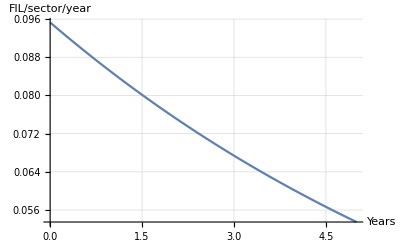

0.824922 (-2^(-t/6)+2^(-tau/6))

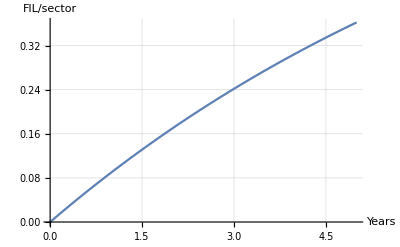

```mathematica
SimpleDecayRate=lambda/.Solve[{Exp[-lambda*6]==1/2,lambda∈Reals},lambda][[1]];(*Per Filecoin spec*)
Current1yRewards=0.09;(*FIL/sector*)
MintingApprox[years_]=Current1yRewards*Exp[-SimpleDecayRate*years]/Integrate[Exp[-SimpleDecayRate*years],{years,0,1}]
Plot[MintingApprox[years],{years,0,5},GridLines->Automatic,AxesLabel->{"Years","FIL/sector/year"}]

Integrate[MintingApprox[years],{years,0,1}];
CumMintingApprox=Integrate[MintingApprox[years],{years,tau,t}]
CumRewardsPerSector[t_,tau_]:=Evaluate@CumMintingApprox
Plot[CumRewardsPerSector[years,0],{years,0,5},GridLines->Automatic,AxesLabel->{"Years","FIL/sector"}]
```

Assume the pledge is fixed at today’s level. This is an okay first approximation. In reality, the shortfall policy is designed to grow onboarding and therefore likely to induce QAP growth and pledge decline.

```mathematica
FullInitialPledge=0.21;(*pledge = 0.21FIL per 32GiB sector*)
```

## Repay the Shortfall (current CNL variant)

### Question 1: How do the Repayment Take, Fee Take, and Ordinary SP Returns, each vary as the shortfall fraction increases?

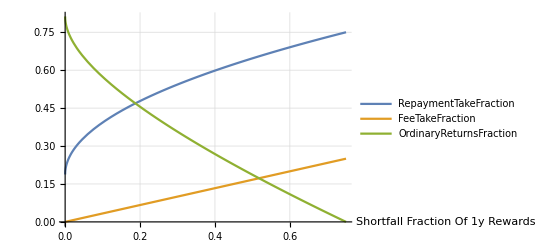

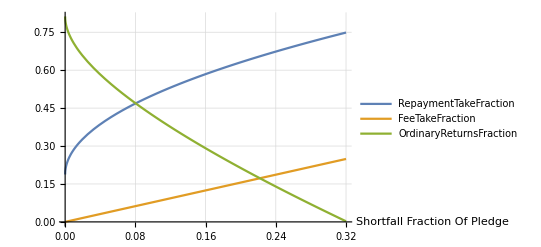

```mathematica
RepaymentTakeFraction[ShortfallFractionOf1yRewards_]:=0.25*0.75+0.75^(3/2)Sqrt[ShortfallFractionOf1yRewards](*Per spec*)
FeeTakeFraction[ShortfallFractionOf1yRewards_]:=ShortfallFractionOf1yRewards/3(*Per spec*)
OrdinaryReturnsFraction[ShortfallFractionOf1yRewards_]:=(1-RepaymentTakeFraction[ShortfallFractionOf1yRewards]-FeeTakeFraction[ShortfallFractionOf1yRewards])

Plot[{RepaymentTakeFraction[ShortfallFractionOf1yRewards],FeeTakeFraction[ShortfallFractionOf1yRewards],OrdinaryReturnsFraction[ShortfallFractionOf1yRewards]},{ShortfallFractionOf1yRewards,0,0.75},PlotLegends->{"RepaymentTakeFraction","FeeTakeFraction","OrdinaryReturnsFraction"},AxesLabel->{"Shortfall Fraction\nOf 1y Rewards"},GridLines->Automatic]

(*In terms of the shortfal fraction, 1y rewards is the natural basis, in this sense this is what the policy specifies the take rates in terms of*)
(*But equally, we need/want to know shortfalls as a function of pledge*)
(*So make a function to convert from one basis to the other*)
ShortfallFractionOfPledgeF[ShortfallFractionOf1yRewards_]:=ShortfallFractionOf1yRewards*CumRewardsPerSector[1,0]/FullInitialPledge
ShortfallFractionOf1yRewardsF[ShortfallFractionOfPledge_]:=ShortfallFractionOfPledge*FullInitialPledge/CumRewardsPerSector[1,0]

Plot[{RepaymentTakeFraction[ShortfallFractionOf1yRewardsF[ShortfallFractionOfPledge]],FeeTakeFraction[ShortfallFractionOf1yRewardsF[ShortfallFractionOfPledge]],OrdinaryReturnsFraction[ShortfallFractionOf1yRewardsF[ShortfallFractionOfPledge]]},{ShortfallFractionOfPledge,0,0.32},PlotLegends->{"RepaymentTakeFraction","FeeTakeFraction","OrdinaryReturnsFraction"},AxesLabel->{"Shortfall Fraction\nOf Pledge"},GridLines->Automatic]
```

### Question 2: How long does it take to repay the shortfall?

More specifically, this is the time to repay a sector, which is onboarded at a given shortfall level,  assuming that miner-level shortfall remains constant throughout the sectors lifetime.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

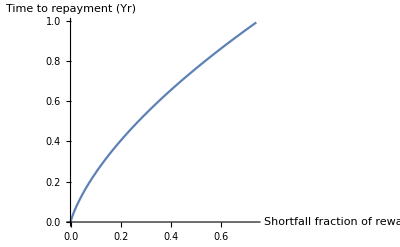

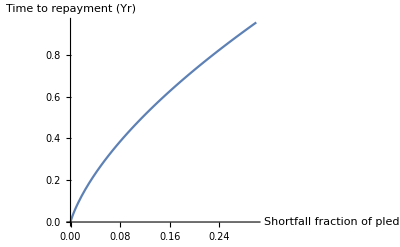

```mathematica
(*Since we've used simple minting which has a simple analytic expression, we can solve and find an expression for the time taken to repay the pledge*)
solnRepaymentTime=Solve[CumRewardsPerSector[RepaymentTime,0]*RepaymentTakeFraction[ShortfallFractionOf1yRewards]-FullInitialPledge*ShortfallFractionOfPledgeF[ShortfallFractionOf1yRewards]==0,RepaymentTime][[1]];

RepaymentTimeRewardsF[shortfall_]:=(RepaymentTime/.solnRepaymentTime)/.{ShortfallFractionOf1yRewards->shortfall}
RepaymentTimePledgeF[ShortfallFractionOfPledge_]:=RepaymentTimeRewardsF[ShortfallFractionOf1yRewardsF[ShortfallFractionOfPledge]]

Plot[RepaymentTimeRewardsF[ShortfallFractionOf1yRewards],{ShortfallFractionOf1yRewards,0,0.74},AxesLabel->{"Shortfall fraction \nof rewards","Time to repayment (Yr)"}]

Plot[RepaymentTimePledgeF[ShortfallFractionOfPledge],{ShortfallFractionOfPledge,0,0.3},AxesLabel->{"Shortfall fraction \nof pledge","Time to repayment (Yr)"}]
```

### Question 3: What do the cumulative Repayment Take, Fee Take and SP Ordinary Returns look like?

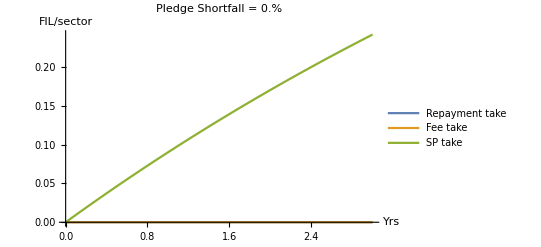
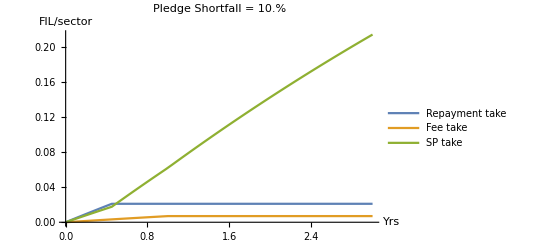
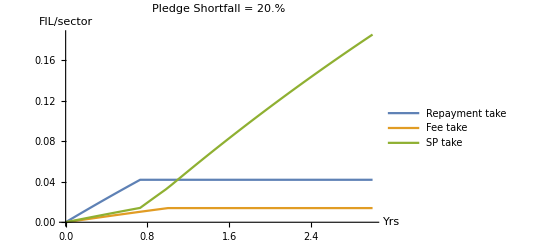
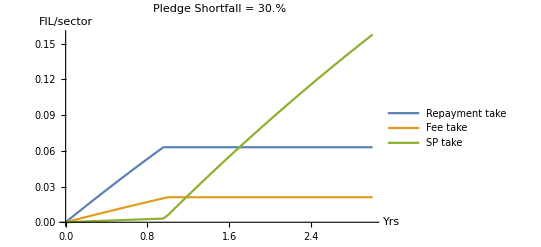

```mathematica
(*The cumulative repayment take is a piecewise function of time*)
(*So long as the repayment take paid does not cover the pledge shortfall, then a fraction of the cumulative rewards --- the repayment take fraction --- goes to paying off the shortfall*)
(*Once the shortfall has been made whole, the cumulative rewards take stops increasing*)
(*The time when it stops accumulating is the time to repayment, for which the function was derived above*)
CumRepaymentTake[t_,ShortfallFractionOf1yRewards_]:=If[CumRewardsPerSector[t,0]*RepaymentTakeFraction[ShortfallFractionOf1yRewards]<FullInitialPledge*ShortfallFractionOfPledgeF[ShortfallFractionOf1yRewards],CumRewardsPerSector[t,0]*RepaymentTakeFraction[ShortfallFractionOf1yRewards],CumRewardsPerSector[RepaymentTimeRewardsF[ShortfallFractionOf1yRewards],0]*RepaymentTakeFraction[ShortfallFractionOf1yRewards]]

CumFeeTake[t_,ShortfallFractionOf1yRewards_,FeeTerm_]:=If[t<FeeTerm,CumRewardsPerSector[t,0]*FeeTakeFraction[ShortfallFractionOf1yRewards],CumRewardsPerSector[FeeTerm,0]*FeeTakeFraction[ShortfallFractionOf1yRewards]]

OrdinaryReturns[t_,ShortfallFractionOf1yRewards_,FeeTerm_]:=CumRewardsPerSector[t,0]-CumFeeTake[t,ShortfallFractionOf1yRewards,FeeTerm]-CumRepaymentTake[t,ShortfallFractionOf1yRewards]

Table[With[{ShortfallFractionOfPledge=i},Plot[{CumRepaymentTake[t,ShortfallFractionOf1yRewardsF[ShortfallFractionOfPledge]],CumFeeTake[t,ShortfallFractionOf1yRewardsF[ShortfallFractionOfPledge],1],OrdinaryReturns[t,ShortfallFractionOf1yRewardsF[ShortfallFractionOfPledge],1]},{t,0,3},PlotRange->All,PlotLegends->{"Repayment take","Fee take","SP take"},PlotLabel->StringJoin[{"Pledge Shortfall = ",ToString@(100*ShortfallFractionOfPledge),"%"}],AxesLabel->{"Yrs","FIL/sector"}]],{i,0,0.3,0.1}]
```

### Q4: How does the returns multiple and annualized FoFR look over time?

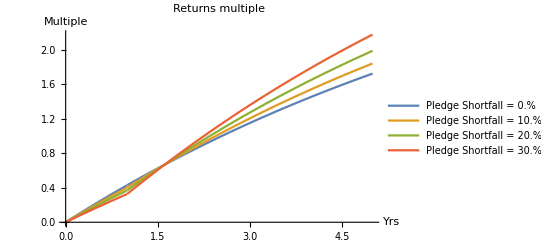

```mathematica
(*Important nNote: Returns are defined as ordinary returns, less the fee take which is burnt, but plus the cumulative repayment take*)
(*The repayment take is added to returns, because it is not included in the principal, but it is received at the end of the commitment*)

(*Second Important Note: the denominator is what was actually put down. This is the full pledge, less the shortfall*)
NetReturnOverCost[t_,ShortfallFractionOf1yRewards_,FeeTerm_]:=(OrdinaryReturns[t,ShortfallFractionOf1yRewards,FeeTerm]+CumRepaymentTake[t,ShortfallFractionOf1yRewards]-CumFeeTake[t,ShortfallFractionOf1yRewards,FeeTerm])/(FullInitialPledge*(1-ShortfallFractionOfPledgeF[ShortfallFractionOf1yRewards]))

Plot[Evaluate@Table[NetReturnOverCost[t,ShortfallFractionOf1yRewardsF[ShortfallFractionOfPledge],1],{ShortfallFractionOfPledge,0,0.3,0.1}],{t,0,5},PlotLegends->Table[StringJoin@{"Pledge Shortfall = ",ToString@(100*ShortfallFractionOfPledge), "%"},{ShortfallFractionOfPledge,0,0.3,0.1}],PlotLabel->"Returns multiple",AxesLabel->{"Yrs","Multiple"}]
```

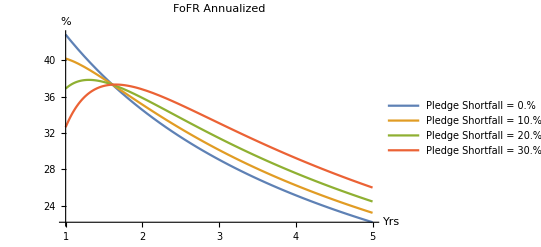

```mathematica
fofrAnnualized[t_,ShortfallFractionOf1yRewards_,FeeTerm_]:=(1+(OrdinaryReturns[t,ShortfallFractionOf1yRewards,FeeTerm]+CumRepaymentTake[t,ShortfallFractionOf1yRewards]-CumFeeTake[t,ShortfallFractionOf1yRewards,FeeTerm])/(FullInitialPledge*(1-ShortfallFractionOfPledgeF[ShortfallFractionOf1yRewards])))^(1/t)-1

Plot[Evaluate@Table[100*fofrAnnualized[t,ShortfallFractionOf1yRewardsF[ShortfallFractionOfPledge],1],{ShortfallFractionOfPledge,0,0.3,0.1}],{t,1,5},PlotLegends->Table[StringJoin@{"Pledge Shortfall = ",ToString@(100*ShortfallFractionOfPledge), "%"},{ShortfallFractionOfPledge,0,0.3,0.1}],PlotLabel->"FoFR Annualized",AxesLabel->{"Yrs","%"}]
```

### Q5: What happens if we make the burn take fee active over the entire lifetime of the commitment not just 1y?

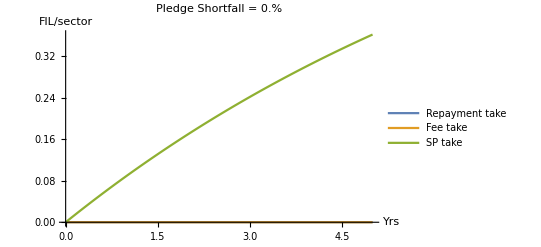
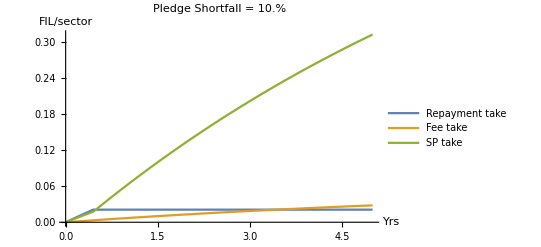
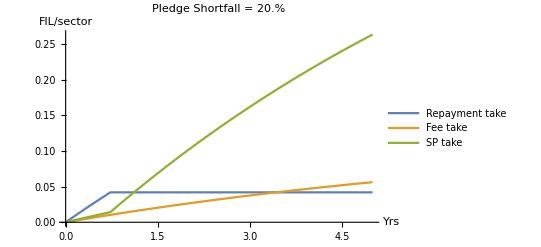
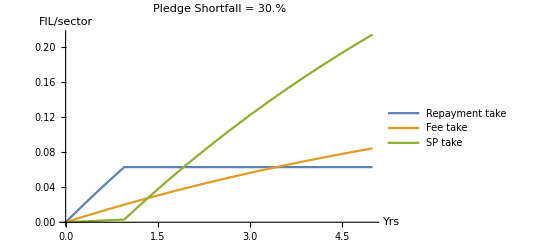

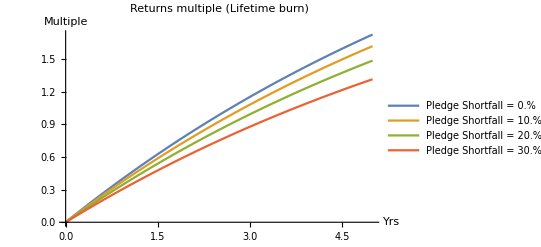

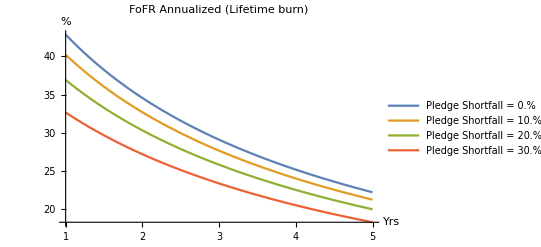

```mathematica
(*Redefine fee dependent functions to give the burn fee a variable term, which we can set to 5y for example*)
Table[With[{ShortfallFractionOfPledge=i},Plot[{CumRepaymentTake[t,ShortfallFractionOf1yRewardsF[ShortfallFractionOfPledge]],CumFeeTake[t,ShortfallFractionOf1yRewardsF[ShortfallFractionOfPledge],5],OrdinaryReturns[t,ShortfallFractionOf1yRewardsF[ShortfallFractionOfPledge],5]},{t,0,5},PlotRange->All,PlotLegends->{"Repayment take","Fee take","SP take"},PlotLabel->StringJoin[{"Pledge Shortfall = ",ToString@(100*ShortfallFractionOfPledge),"%"}],AxesLabel->{"Yrs","FIL/sector"}]],{i,0,0.3,0.1}]

Plot[Evaluate@Table[NetReturnOverCost[t,ShortfallFractionOf1yRewardsF[ShortfallFractionOfPledge],5],{ShortfallFractionOfPledge,0,0.3,0.1}],{t,0,5},PlotLegends->Table[StringJoin@{"Pledge Shortfall = ",ToString@(100*ShortfallFractionOfPledge), "%"},{ShortfallFractionOfPledge,0,0.3,0.1}],PlotLabel->"Returns multiple (Lifetime burn)",AxesLabel->{"Yrs","Multiple"}]

Plot[Evaluate@Table[100*fofrAnnualized[t,ShortfallFractionOf1yRewardsF[ShortfallFractionOfPledge],5],{ShortfallFractionOfPledge,0,0.3,0.1}],{t,1,5},PlotLegends->Table[StringJoin@{"Pledge Shortfall = ",ToString@(100*ShortfallFractionOfPledge), "%"},{ShortfallFractionOfPledge,0,0.3,0.1}],PlotLabel->"FoFR Annualized (Lifetime burn)",AxesLabel->{"Yrs","%"}]
```

### Q6: What happens if we make the burn take fee active until the amount borrowed is burnt?

### Q7: what is the deflationary impact of the policy?

Assumption: investment inflow remains at the current level. It doesn’t drop back because data onboarding becomes more of a constrain the FIL availability.

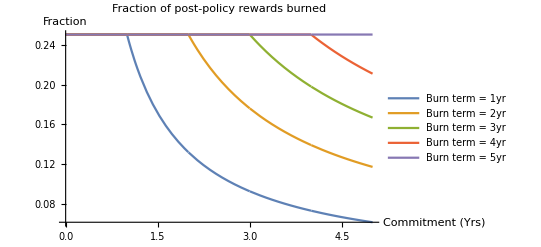

```mathematica
Plot[Evaluate@Table[CumFeeTake[t,0.75,burnterm]/CumRewardsPerSector[t,0],{burnterm,1,5}],{t,0,5},PlotLabel->"Fraction of post-policy rewards burned",PlotLegends->Table[StringJoin@{"Burn term = ",ToString@burnterm, "yr"},{burnterm,1,5}],AxesLabel->{"Commitment (Yrs)","Fraction"}]
```

## Burn the Shortfall

### Q1: How does the a single sector balance look in Burn the Shortfall?

Note: Acknowledge that miner-level aggregation is a critical part of this policy, but what happens with a single is still an important limit to understand.

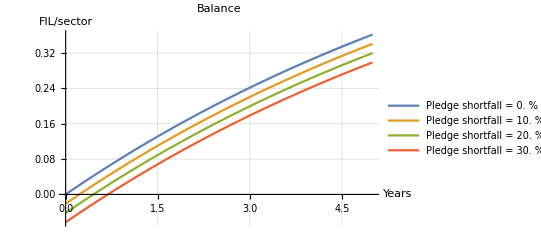

```mathematica
BalancePerSector[BorrowFraction_,t_,tau_]:=If[t<tau,0,CumRewardsPerSector[t,tau]-FullInitialPledge*BorrowFraction]
Plot[Evaluate@Table[BalancePerSector[pledgeshortfall,t,0],{pledgeshortfall,0,0.3,0.1}],{t,0,5},AxesLabel->{"Years","FIL/sector"},GridLines->Automatic,PlotLabel->"Balance",PlotLegends->Table[StringJoin@{"Pledge shortfall = ",ToString@(100*pledgeshortfall)," %"},{pledgeshortfall,0,0.3,0.1}]]
```

### Q2: What are the returns multiple and annualized returns?

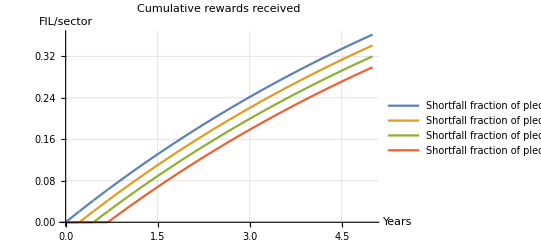

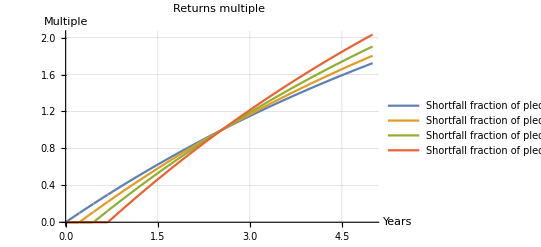

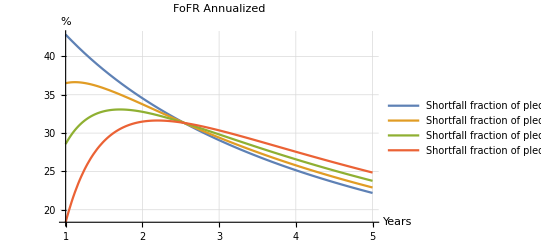

```mathematica
CumRewardsPerSectorReceived[BorrowFraction_,t_,tau_]:=If[CumRewardsPerSector[t,tau]<FullInitialPledge*BorrowFraction,0,CumRewardsPerSector[t,tau]-FullInitialPledge*BorrowFraction]
Plot[Evaluate@Table[CumRewardsPerSectorReceived[BorrowFraction,t,0],{BorrowFraction,0,0.3,0.1}],{t,0,5},AxesLabel->{"Years","FIL/sector"},PlotLegends->Table[StringJoin[{"Shortfall fraction of pledge = ",ToString@(100*BorrowFraction)," %"}],{BorrowFraction,0,0.5,0.1}],GridLines->Automatic,PlotLabel->"Cumulative rewards received"]

BSReturnMultiple[BorrowFraction_,t_]:=CumRewardsPerSectorReceived[BorrowFraction,t,0]/(FullInitialPledge(1-BorrowFraction))
Plot[Evaluate@Table[BSReturnMultiple[BorrowFraction,t],{BorrowFraction,0,0.3,0.1}],{t,0,5},AxesLabel->{"Years","Multiple"},PlotLegends->Table[StringJoin[{"Shortfall fraction of pledge = ",ToString@(100*BorrowFraction)," %"}],{BorrowFraction,0,0.3,0.1}],GridLines->Automatic,PlotLabel->"Returns multiple"]

BSFoFRAnnualized[BorrowFraction_,t_,tau_]:=(1+CumRewardsPerSectorReceived[BorrowFraction,t,tau]/(FullInitialPledge(1-BorrowFraction)))^(1/t)-1
Plot[Evaluate@Table[100*BSFoFRAnnualized[BorrowFraction,t,0],{BorrowFraction,0,0.3,0.1}],{t,1,5},AxesLabel->{"Years","%"},PlotLegends->Table[StringJoin[{"Shortfall fraction of pledge = ",ToString@(100*BorrowFraction)," %"}],{BorrowFraction,0,0.3,0.1}],GridLines->Automatic,PlotLabel->"FoFR Annualized",PlotRange->All]
```

### Q3: What is the burn impact?

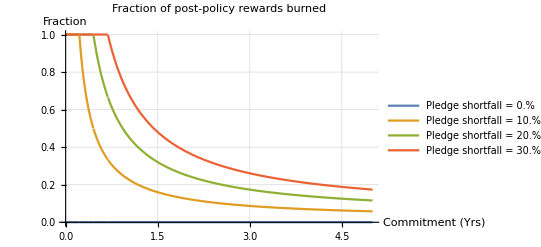

```mathematica
BSBurn[BorrowFraction_,t_,tau_]:=If[CumRewardsPerSector[t,tau]<FullInitialPledge*BorrowFraction,CumRewardsPerSector[t,tau],FullInitialPledge*BorrowFraction]

Plot[Evaluate@Table[BSBurn[BorrowFraction,t,0]/CumRewardsPerSector[t,0],{BorrowFraction,0,0.3,0.1}],{t,0,5},PlotLabel->"Fraction of post-policy rewards burned",PlotLegends->Table[StringJoin@{"Pledge shortfall = ",ToString@(100*BorrowFraction), "%"},{BorrowFraction,0,0.3,0.1}],AxesLabel->{"Commitment (Yrs)","Fraction"},GridLines->Automatic]
```

### Q5: What is the effect of aggregation of sectors?

### Q5A: Effect uniform linear onboarding at different shortfall fractions:

#### 20% pledge shortfall

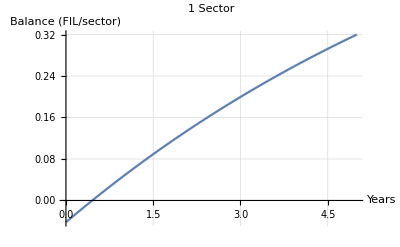

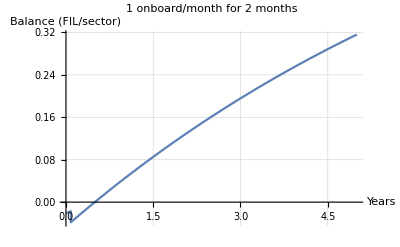

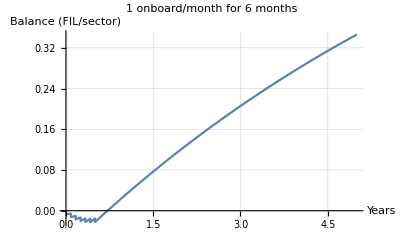

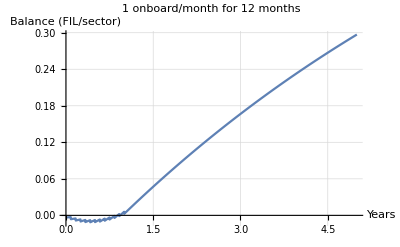

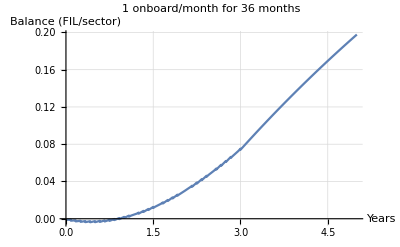

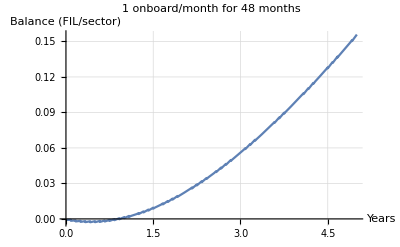

```mathematica
shortfalltemp=0.2;
Plot[Sum[BalancePerSector[shortfalltemp,t,tau],{tau,0,0,1/12}],{t,0,5},AxesLabel->{"Years","Balance (FIL/sector)"},GridLines->Automatic,PlotLabel->"1 Sector"]
Plot[Sum[BalancePerSector[shortfalltemp,t,tau],{tau,0,1/12,1/12}]/2,{t,0,5},AxesLabel->{"Years","Balance (FIL/sector)"},GridLines->Automatic,PlotLabel->"1 onboard/month for 2 months"]
Plot[Sum[BalancePerSector[shortfalltemp,t,tau],{tau,0,0.5,1/12}]/6,{t,0,5},AxesLabel->{"Years","Balance (FIL/sector)"},GridLines->Automatic,PlotLabel->"1 onboard/month for 6 months"]
Plot[Sum[BalancePerSector[shortfalltemp,t,tau],{tau,0,1,1/12}]/12,{t,0,5},AxesLabel->{"Years","Balance (FIL/sector)"},GridLines->Automatic,PlotLabel->"1 onboard/month for 12 months"]
Plot[Sum[BalancePerSector[shortfalltemp,t,tau],{tau,0,3,1/12}]/36,{t,0,5},AxesLabel->{"Years","Balance (FIL/sector)"},GridLines->Automatic,PlotLabel->"1 onboard/month for 36 months"]
Plot[Sum[BalancePerSector[shortfalltemp,t,tau],{tau,0,5,1/12}]/48,{t,0,5},AxesLabel->{"Years","Balance (FIL/sector)"},GridLines->Automatic,PlotLabel->"1 onboard/month for 48 months"]
```

## 10% pledge shortfall

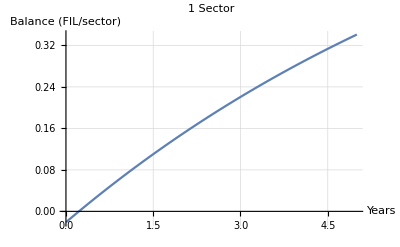

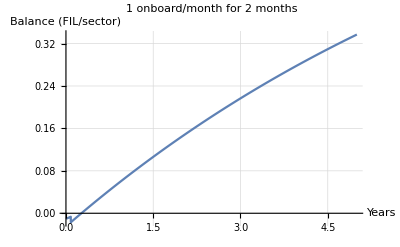

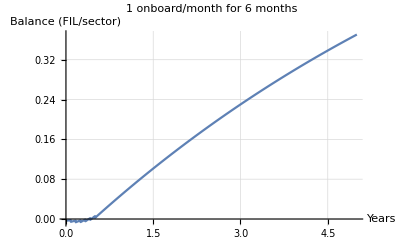

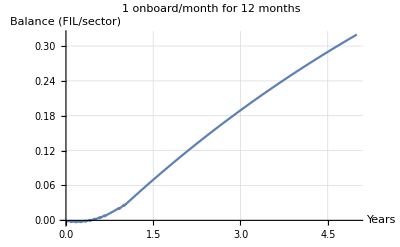

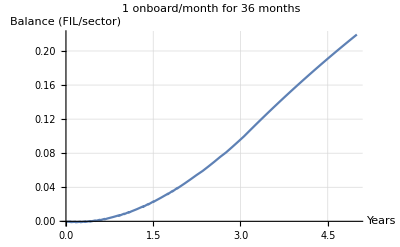

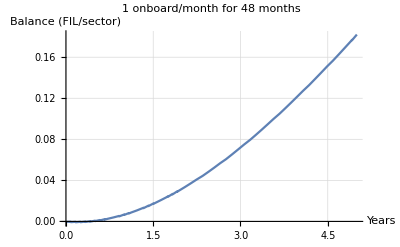

```mathematica
shortfalltemp=0.1;
Plot[Sum[BalancePerSector[shortfalltemp,t,tau],{tau,0,0,1/12}],{t,0,5},AxesLabel->{"Years","Balance (FIL/sector)"},GridLines->Automatic,PlotLabel->"1 Sector"]
Plot[Sum[BalancePerSector[shortfalltemp,t,tau],{tau,0,1/12,1/12}]/2,{t,0,5},AxesLabel->{"Years","Balance (FIL/sector)"},GridLines->Automatic,PlotLabel->"1 onboard/month for 2 months"]
Plot[Sum[BalancePerSector[shortfalltemp,t,tau],{tau,0,0.5,1/12}]/6,{t,0,5},AxesLabel->{"Years","Balance (FIL/sector)"},GridLines->Automatic,PlotLabel->"1 onboard/month for 6 months"]
Plot[Sum[BalancePerSector[shortfalltemp,t,tau],{tau,0,1,1/12}]/12,{t,0,5},AxesLabel->{"Years","Balance (FIL/sector)"},GridLines->Automatic,PlotLabel->"1 onboard/month for 12 months"]
Plot[Sum[BalancePerSector[shortfalltemp,t,tau],{tau,0,3,1/12}]/36,{t,0,5},AxesLabel->{"Years","Balance (FIL/sector)"},GridLines->Automatic,PlotLabel->"1 onboard/month for 36 months"]
Plot[Sum[BalancePerSector[shortfalltemp,t,tau],{tau,0,5,1/12}]/48,{t,0,5},AxesLabel->{"Years","Balance (FIL/sector)"},GridLines->Automatic,PlotLabel->"1 onboard/month for 48 months"]
```

#### 30% pledge shortfall

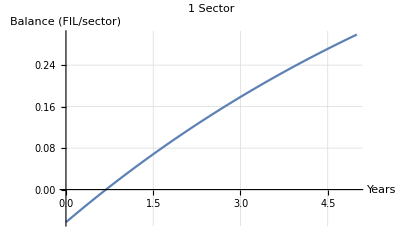

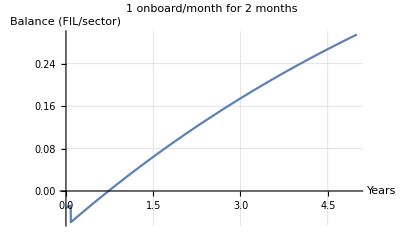

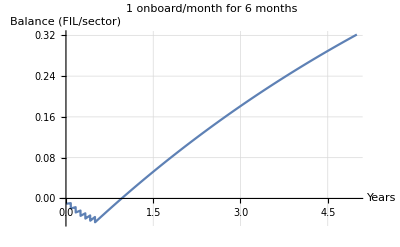

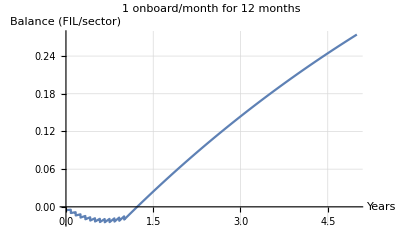

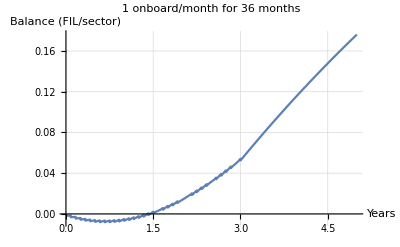

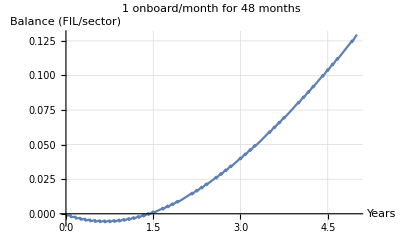

```mathematica
shortfalltemp=0.3;
Plot[Sum[BalancePerSector[shortfalltemp,t,tau],{tau,0,0,1/12}],{t,0,5},AxesLabel->{"Years","Balance (FIL/sector)"},GridLines->Automatic,PlotLabel->"1 Sector"]
Plot[Sum[BalancePerSector[shortfalltemp,t,tau],{tau,0,1/12,1/12}]/2,{t,0,5},AxesLabel->{"Years","Balance (FIL/sector)"},GridLines->Automatic,PlotLabel->"1 onboard/month for 2 months"]
Plot[Sum[BalancePerSector[shortfalltemp,t,tau],{tau,0,0.5,1/12}]/6,{t,0,5},AxesLabel->{"Years","Balance (FIL/sector)"},GridLines->Automatic,PlotLabel->"1 onboard/month for 6 months"]
Plot[Sum[BalancePerSector[shortfalltemp,t,tau],{tau,0,1,1/12}]/12,{t,0,5},AxesLabel->{"Years","Balance (FIL/sector)"},GridLines->Automatic,PlotLabel->"1 onboard/month for 12 months"]
Plot[Sum[BalancePerSector[shortfalltemp,t,tau],{tau,0,3,1/12}]/36,{t,0,5},AxesLabel->{"Years","Balance (FIL/sector)"},GridLines->Automatic,PlotLabel->"1 onboard/month for 36 months"]
Plot[Sum[BalancePerSector[shortfalltemp,t,tau],{tau,0,5,1/12}]/48,{t,0,5},AxesLabel->{"Years","Balance (FIL/sector)"},GridLines->Automatic,PlotLabel->"1 onboard/month for 48 months"]
```

### Q5B: What’s the effect of non-linear onboarding schedule:

#### Different onboarding schedules

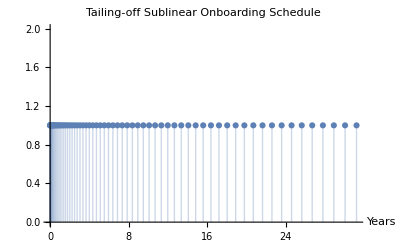

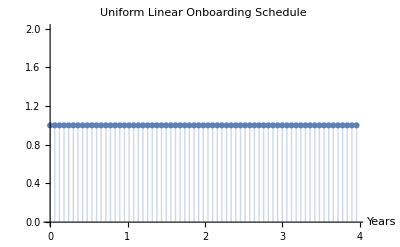

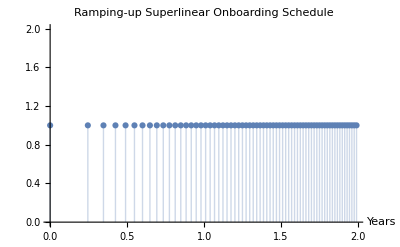

```mathematica
ScheduleMaxDur=4;
SublinearOnboardingSchedule=Table[i^2.5
,{i,0,ScheduleMaxDur,0.06}];
ListPlot[Transpose@{SublinearOnboardingSchedule,Table[1,{i,1,Length@SublinearOnboardingSchedule}]},Filling->Axis,AxesLabel->{"Years",""},PlotLabel->"Tailing-off Sublinear Onboarding Schedule"]

LinearOnboardingSchedule=Table[i
,{i,0,ScheduleMaxDur,0.06}];
ListPlot[Transpose@{LinearOnboardingSchedule,Table[1,{i,1,Length@LinearOnboardingSchedule}]},Filling->Axis,AxesLabel->{"Years",""},PlotLabel->"Uniform Linear Onboarding Schedule"]

SuperlinearOnboardingSchedule=Table[i^0.5
,{i,0,ScheduleMaxDur,0.06}];
ListPlot[Transpose@{SuperlinearOnboardingSchedule,Table[1,{i,1,Length@SuperlinearOnboardingSchedule}]},Filling->Axis,AxesLabel->{"Years",""},PlotLabel->"Ramping-up Superlinear Onboarding Schedule"]
```

#### Effect on the aggregate average per sector balance and time to breakeven on the shortfall

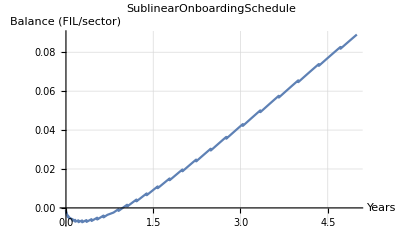

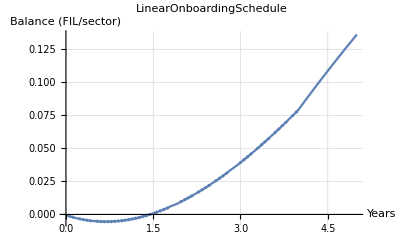

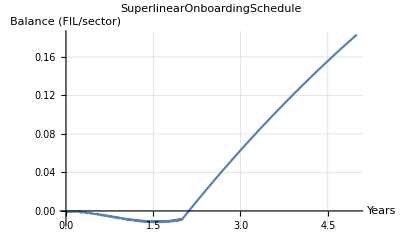

```mathematica
With[{schedule=SublinearOnboardingSchedule,name="SublinearOnboardingSchedule"},Plot[Sum[BalancePerSector[shortfalltemp,t,schedule[[taui]]],{taui,1,Length@schedule}]/(Length@schedule),{t,0,5},AxesLabel->{"Years","Balance (FIL/sector)"},GridLines->Automatic,PlotLabel->ToString@name]]

With[{schedule=LinearOnboardingSchedule,name="LinearOnboardingSchedule"},Plot[Sum[BalancePerSector[shortfalltemp,t,schedule[[taui]]],{taui,1,Length@schedule}]/(Length@schedule),{t,0,5},AxesLabel->{"Years","Balance (FIL/sector)"},GridLines->Automatic,PlotLabel->ToString@name]]

With[{schedule=SuperlinearOnboardingSchedule,name="SuperlinearOnboardingSchedule"},Plot[Sum[BalancePerSector[shortfalltemp,t,schedule[[taui]]],{taui,1,Length@schedule}]/(Length@schedule),{t,0,5},AxesLabel->{"Years","Balance (FIL/sector)"},GridLines->Automatic,PlotLabel->ToString@name]]
```

### Q5C: What’s the ROI with on an aggregate of sectors

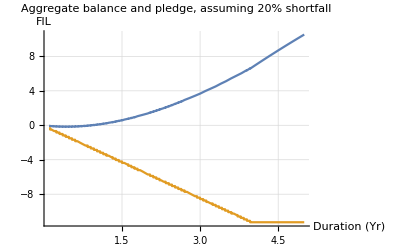

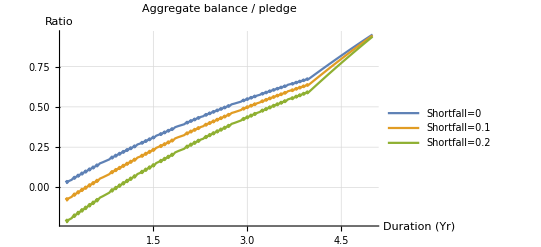

```mathematica
(*Assume 20% shortfall, and continuous linear onboarding for 4y*)
ShortFallPledge[BorrowFraction_]:=FullInitialPledge*(1-BorrowFraction)
AggShortfallPledge[BorrowFraction_,tt_]:=Length[Select[LinearOnboardingSchedule,#<tt&]]*ShortFallPledge[BorrowFraction]
AggBalancePerSector[BorrowFraction_,t_]:=Sum[BalancePerSector[BorrowFraction,t,LinearOnboardingSchedule[[i]]],{i,1,Length@LinearOnboardingSchedule}]

With[{shortfallTest=0.2},Plot[{AggBalancePerSector[shortfallTest,t],-AggShortfallPledge[shortfallTest,t]},{t,0.1,5},PlotRange->All,PerformanceGoal->"Quality",AxesLabel->{"Duration (Yr)","FIL"},GridLines->Automatic,PlotLabel->"Aggregate balance and pledge, assuming 20% shortfall"]]


Plot[{AggBalancePerSector[0,t]/AggShortfallPledge[0,t],AggBalancePerSector[0.1,t]/AggShortfallPledge[0.1,t],AggBalancePerSector[0.2,t]/AggShortfallPledge[0.2,t]},{t,0.1,5},AxesLabel->{"Duration (Yr)","Ratio"},PlotLegends->{"Shortfall=0","Shortfall=0.1","Shortfall=0.2"},GridLines->Automatic,PlotLabel->"Aggregate balance / pledge"]
```

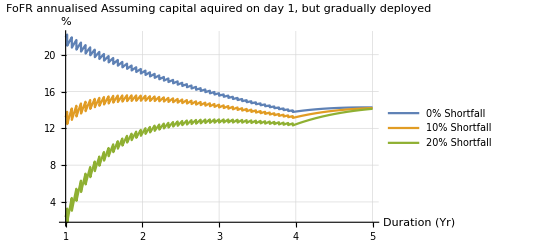

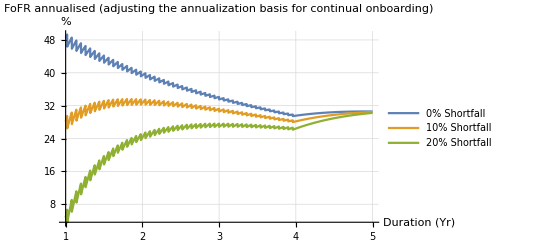

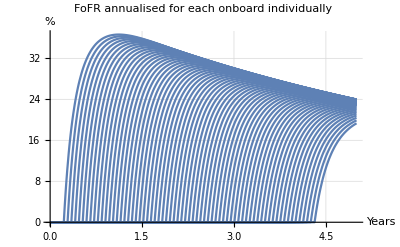

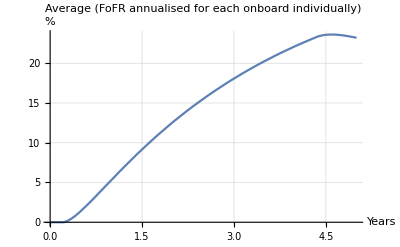

```mathematica
AnnualisedFoFRAgg[BorrowFraction_?NumericQ,t_?NumericQ,timeBasisAdjustment_]:=
((AggShortfallPledge[BorrowFraction,t]+AggBalancePerSector[BorrowFraction,t])/AggShortfallPledge[BorrowFraction,t])^(1/(t*timeBasisAdjustment))-1

Plot[{100*AnnualisedFoFRAgg[0,t,1],100*AnnualisedFoFRAgg[0.1,t,1],100*AnnualisedFoFRAgg[0.2,t,1]},{t,1,5},PlotRange->All,PlotLegends->{"0% Shortfall","10% Shortfall","20% Shortfall"},GridLines->Automatic,AxesLabel->{"Duration (Yr)","%"},PlotLabel->"FoFR annualised\n Assuming capital aquired on day 1, but gradually deployed",PerformanceGoal->"Quality"]

(*Adjust*)
Plot[{100*AnnualisedFoFRAgg[0,t,0.5],100*AnnualisedFoFRAgg[0.1,t,0.5],100*AnnualisedFoFRAgg[0.2,t,0.5]},{t,1,5},PlotRange->All,PlotLegends->{"0% Shortfall","10% Shortfall","20% Shortfall"},GridLines->Automatic,AxesLabel->{"Duration (Yr)","%"},PlotLabel->"FoFR annualised \n(adjusting the annualization basis for continual onboarding)",PerformanceGoal->"Quality"]

BSFoFRAnnualizedAgg[BorrowFraction_,t_,tau_]:=(1+CumRewardsPerSectorReceived[BorrowFraction,t,tau]/(FullInitialPledge(1-BorrowFraction)))^(1/(t-tau))-1
disagAccountingv3ROIannualized[BorrowFraction_,t_,tau_]:=(((FullInitialPledge*(1-BorrowFraction)+CumRewardsPerSectorReceived[BorrowFraction,t,tau])/(FullInitialPledge(1-BorrowFraction)))^(1/(t-tau))-1)
disagAccountingv3ROIannualized[BorrowFraction_,t_]:=Table[BSFoFRAnnualizedAgg[BorrowFraction,t,LinearOnboardingSchedule[[taui]]],{taui,1,Length@LinearOnboardingSchedule}]

Plot[100*disagAccountingv3ROIannualized[0.1,t],{t,0,5},GridLines->Automatic,AxesLabel->{"Years","%"},PlotLabel->"FoFR annualised for each onboard individually",PerformanceGoal->"Quality"]
Plot[100*Mean@disagAccountingv3ROIannualized[0.1,t],{t,0,5},GridLines->Automatic,AxesLabel->{"Years","%"},PlotLabel->"Average (FoFR annualised for each onboard individually)",PerformanceGoal->"Quality"]
```

## Burn the Shortfall V2 (Softer trickle back variant)

### Q1: What the returns multiple and annualized returns?

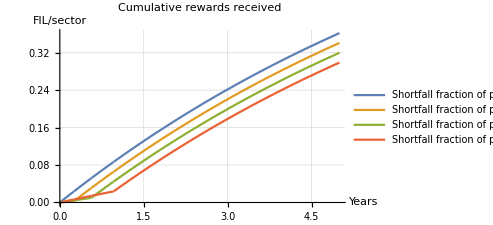

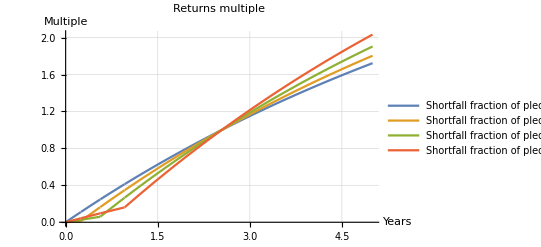

-Graphics-

```mathematica
TrickleBack[BorrowFraction_,t_,tau_]:=BorrowFraction*CumRewardsPerSector[t,tau]*(1-BorrowFraction^2)
CumRewardsPerSectorReceived2[BorrowFraction_,t_,tau_]:=If[CumRewardsPerSector[t,tau]-TrickleBack[BorrowFraction,t,tau]<FullInitialPledge*BorrowFraction,TrickleBack[BorrowFraction,t,tau],CumRewardsPerSector[t,tau]-FullInitialPledge*BorrowFraction]

Plot[Evaluate@Table[CumRewardsPerSectorReceived2[BorrowFraction,t,0],{BorrowFraction,0,0.3,0.1}],{t,0,5},AxesLabel->{"Years","FIL/sector"},PlotLegends->Table[StringJoin[{"Shortfall fraction of pledge = ",ToString@(100*BorrowFraction)," %"}],{BorrowFraction,0,0.5,0.1}],GridLines->Automatic,PlotLabel->"Cumulative rewards received"]

BSReturnMultiple[BorrowFraction_,t_]:=CumRewardsPerSectorReceived2[BorrowFraction,t,0]/(FullInitialPledge(1-BorrowFraction))
Plot[Evaluate@Table[BSReturnMultiple[BorrowFraction,t],{BorrowFraction,0,0.3,0.1}],{t,0,5},AxesLabel->{"Years","Multiple"},PlotLegends->Table[StringJoin[{"Shortfall fraction of pledge = ",ToString@(100*BorrowFraction)," %"}],{BorrowFraction,0,0.3,0.1}],GridLines->Automatic,PlotLabel->"Returns multiple"]

BSFoFRAnnualized[BorrowFraction_,t_]:=(1+CumRewardsPerSectorReceived2[BorrowFraction,t,0]/(FullInitialPledge(1-BorrowFraction)))^(1/t)-1
Plot[Evaluate@Table[100*BSFoFRAnnualized[BorrowFraction,t],{BorrowFraction,0,0.3,0.1}],{t,1,5},AxesLabel->{"Years","%"},PlotLegends->Table[StringJoin[{"Shortfall fraction of pledge = ",ToString@(100*BorrowFraction)," %"}],{BorrowFraction,0,0.3,0.1}],GridLines->Automatic,PlotLabel->"FoFR Annualized",PlotRange->All]
```

### Q2: What’s the burn impact?

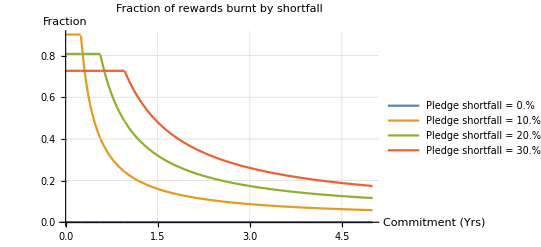

```mathematica
BSBurn2[BorrowFraction_,t_,tau_]:=If[CumRewardsPerSector[t,tau]-TrickleBack[BorrowFraction,t,tau]<FullInitialPledge*BorrowFraction,CumRewardsPerSector[t,tau]-TrickleBack[BorrowFraction,t,tau],FullInitialPledge*BorrowFraction]

Plot[Evaluate@Table[BSBurn2[BorrowFraction,t,0]/CumRewardsPerSector[t,0],{BorrowFraction,0,0.3,0.1}],{t,0,5},PlotLabel->"Fraction of rewards burnt by shortfall",PlotLegends->Table[StringJoin@{"Pledge shortfall = ",ToString@(100*BorrowFraction), "%"},{BorrowFraction,0,0.3,0.1}],AxesLabel->{"Commitment (Yrs)","Fraction"},GridLines->Automatic]
```